## Зависимости спектра и запрещенной зоны от параметров потенциала

```mathematica
(*Globals*)
ℏ=QuantityMagnitude[UnitConvert[Quantity[1/(2π),"PlanckConstant"]]];
m=0.19*QuantityMagnitude[UnitConvert[Quantity[1,"ElectronMass"]]];
e=QuantityMagnitude[UnitConvert[Quantity[1,"ElementaryCharge"]]];
α[Energy_]:=√((2*m*Energy*e)/ℏ^2);
β[Energy_,V_]:=√((2m(Energy+V)*e)/ℏ^2);
KronigPenney[Energy_,V_]:=1/a*ArcCos[(Cos[β[Energy,V]*b]*Cos[α[Energy]*(a-b)])-(α[Energy]^2+β[Energy,V]^2)/(2*α[Energy]*β[Energy,V])*Sin[β[Energy,V]*b]*Sin[α[Energy]*(a-b)]];
PlotFunc[av_,bv_,Energy_,V_]:={Transpose[{Re[KronigPenney[Energy,V]],Energy}],Transpose[{-Re[KronigPenney[Energy,V]],Energy}]}/.{a->av,b->bv};
```

```mathematica
plotter[a_,b_,V_]:=Show[ListPlot[{{a*10^9-b*10^9/2,1},{2a*10^9-b*10^9/2,1}},PlotRange->{{0,2a*10^9},{2,-V}},PlotMarkers->{Automatic, Medium},AxesLabel->{"x*10^-9, м","V(x), эВ"}],ListPlot[{{a*10^9-b*10^9/2,1.5},{2a*10^9-b*10^9/2,1.5*V}},PlotMarkers->"Z^+",PlotStyle->Black],Graphics[Line[{
{0,0},{a*10^9-b*10^9,0},{a*10^9-b*10^9,-V},{a*10^9,-V},{a*10^9,0},
{a*10^9,0},{2a*10^9-b*10^9,0},{2a*10^9-b*10^9,-V},{2a*10^9,-V},{2a*10^9,0},
{2a*10^9,0},{3a*10^9-b*10^9,0},{3a*10^9-b*10^9,-V},{3a*10^9,-V},{3a*10^9,0}
}]]];
```

```mathematica
manip=Manipulate[
{plotter[a,b,V],ListLinePlot[PlotFunc[a,b,Range[0.01,50,0.01],V],PlotStyle->Blue,PlotRange->Full,AxesLabel->{"ka, (:043c)^-1","E, эВ"}]},{a,0.1*10^-9,1*10^-9},{b,0*10^-9,a},{V,1,100}
]
```

## Зависимость ширины запрещенной зоны от ширины потенциальной ямы

```mathematica
Manipulate[Plot[Re[KronigPenney[Energy,10]]/.{a->0.9*10^-9,b->bv},{Energy,-1,30},PlotRange->{{0-1,30},{0,3.5*10^9}},AxesLabel->{"E","k"}],{bv,0,0.9*10^-9}]
```

```mathematica
(*Функция ширины запрещенной зоны*)
BandGap[bv_]:=Position[Re[KronigPenney[Range[0.01,10,0.01],10]/.{a->0.9/10^9,b->bv}],x_/;TrueQ[x≠0]][[Min[Position[Re[KronigPenney[Range[0.01,10,0.01],10]/.{a->0.9*10^-9,b->bv}],0.]]]][[1]]*0.01-Min[Position[Re[KronigPenney[Range[0.01,10,0.01],10]/.{a->0.9*10^-9,b->bv}],0.]]*0.01;
```

```mathematica
gapWidthOfB=Table[BandGap[b],{b,0.02*10^-9,0.88*10^-9,0.01*10^-9}];
```

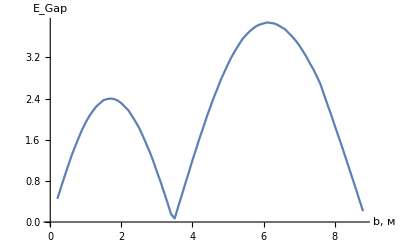

```mathematica
ListLinePlot[Transpose[{Range[0.02*10^-9,0.88*10^-9,0.01*10^-9],gapWidthOfB}],AxesLabel->{"b, м","E_Gap, эВ"}]
```

## Зависимость эффективной массы для разрешенной зоны от ширины потенциальной ямы

```mathematica
AccessGap[bv_]:=Range[0.01,30,0.01][[Position[Re[KronigPenney[Range[0.01,30,0.01],10]/.{a->0.9/10^9,b->bv}],Max[Re[KronigPenney[Range[0.01,30,0.01],10]/.{a->0.9/10^9,b->bv}]]][[1,1]]]]-Range[0.01,30,0.01][[Max[Position[Re[KronigPenney[Range[0.01,10,0.01],10]/.{a->0.9*10^-9,b->bv}],0.]]]];
```

```mathematica
accessWidthOfB=Table[AccessGap[b],{b,0.02*10^-9,0.88*10^-9,0.01*10^-9}];
```

```mathematica
maxTop=Max[Re[KronigPenney[Range[0.01,30,0.01],10]/.{a->0.9/10^9,b->6*10^-10}]];
topPos[bv_]:=Range[0.01,30,0.01][[Min[Select[Transpose[Position[Re[KronigPenney[Range[0.01,30,0.01],10]/.{a->0.9/10^9,b->bv}], x_/;TrueQ[3.486*10^9≤ x≤maxTop]]][[1]],#>1000&]]]];
topPosTab=Table[topPos[b],{b,0.02*10^-9,0.88*10^-9,0.01*10^-9}];
```

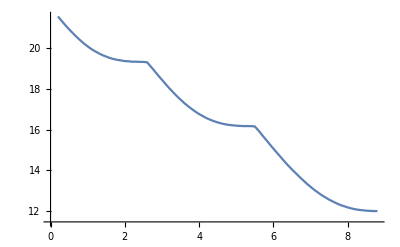

```mathematica
ListLinePlot[Transpose[{Range[0.02*10^-9,0.88*10^-9,0.01*10^-9],topPosTab}]]
```

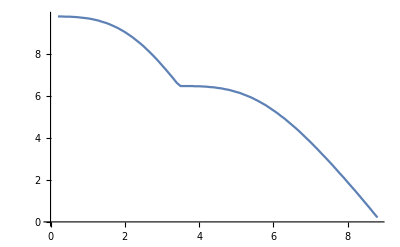

```mathematica
lowPos[bv_]:=Range[0.01,30,0.01][[Max[Position[Re[KronigPenney[Range[0.01,10,0.01],10]/.{a->0.9*10^-9,b->bv}],0.]]]];
lowPosTab=Table[lowPos[b],{b,0.02*10^-9,0.88*10^-9,0.01*10^-9}];
ListLinePlot[Transpose[{Range[0.02*10^-9,0.88*10^-9,0.01*10^-9],lowPosTab}]]
```

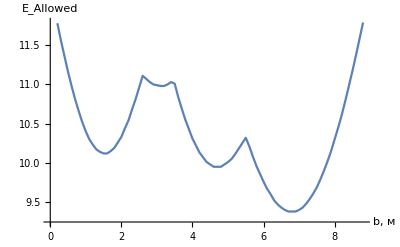

```mathematica
ListLinePlot[Transpose[{Range[0.02*10^-9,0.88*10^-9,0.01*10^-9],topPosTab-lowPosTab}],AxesLabel->{"b, м","E_Allowed, эВ"}]
```

```mathematica
maxTop
```

3.49066×10^9

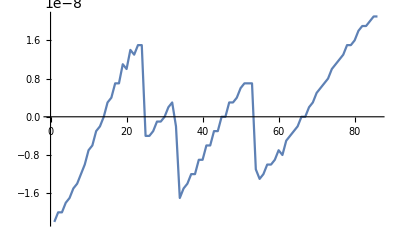

```mathematica
deriv={};
For[i=2,i≤Length[topPosTab-lowPosTab],i++,
AppendTo[deriv,((topPosTab-lowPosTab)[[i]]-(topPosTab-lowPosTab)[[i-1]])/0.01*10^-9]
]
ListLinePlot[deriv]
deriv2={};
For[i=2,i≤Length[deriv],i++,
AppendTo[deriv2,(deriv[[i]]-deriv[[i-1]])/0.01*10^-9]
]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

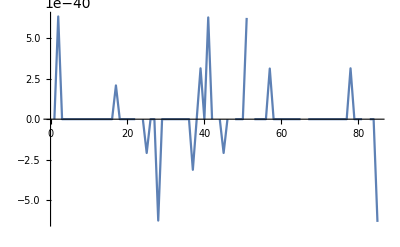

```mathematica
ListLinePlot[ℏ^2 deriv2^-1,PlotRange->Full]
```